```mathematica
Alpha0z
```

```mathematica
Clear[Xi,z,r]
r=Alpha0z;
z=x+I*y;
C
```

ArcCosh[(1.13953+0. ⅈ) (-1.2+z)]

```mathematica
Re[Alpha0z]
```

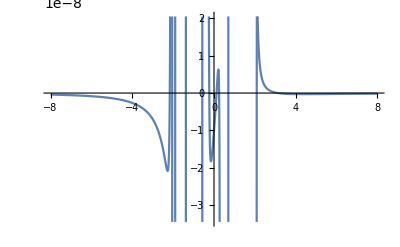

```mathematica
Plot[%136,{z,-8,8}]
```

```mathematica
BetaFarz[2]
```

0

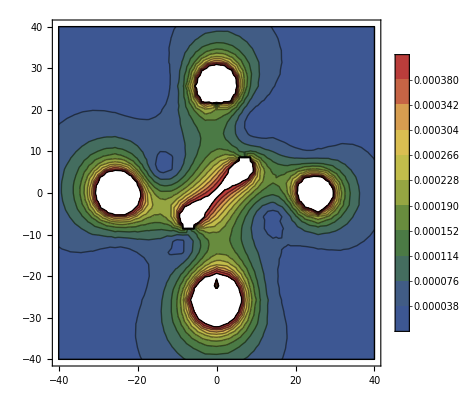

```mathematica
ClearSystemCache[]
Clear[s11z,s12z,s22z,z,size]
size=40;
s11z=Sigma11ztot;
s12z=Sigma12ztot;
s22z=Sigma22ztot;
z=x+I*y;
s22z;
s12z;
s11z;
smv= Sqrt[s11z*s11z+s22z*s22z-s11z*s22z+3s12z*s12z];

c1=10;
Clear[q,q1,q2,q3,q4]
q=1;q1=2;q2=3;q3=4;q4=5;

ContourPlot[smv,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1]
```

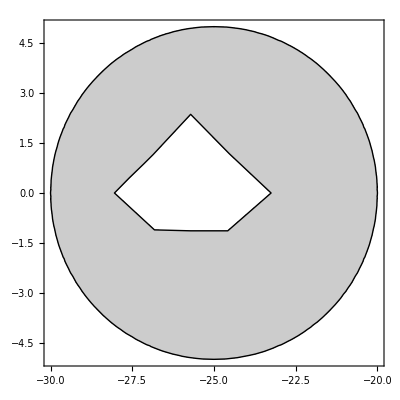

```mathematica
Clear[PhiQInside,PsiQInside,AlphaQ,BetaQ0]
(*dminus[i_,q_]:=Module[{f},f=abmnpq`d[i,q]-2 i Sinh[2*Zeta0[q]] abmnpq`c[i,q]]*)
PhiQInside[q_] := Module[{f,v}, 
v = Exp[XiQ[q]]; f =  Sum[abmnpq`c[i, q] (v^i + v^(-i)) , {i, n}]] 

PsiQInside[q_] := 
 Module[{f, f1, Psi0, Psi1,v}, 
   v = Exp[XiQ[q]];
  f1 = (Sinh[Zeta0[q]] /Sinh[XiQ[q]]) (v/v0[q] - v0[q]/v);Psi0 = Sum[abmnpq`dminus[i, q] v^(i) + abmnpq`d[i, q] v^(-i), {i, n}]; 
  Psi1 = Sum[ i f1 abmnpq`c[i, q] ( v^(-i) - v^(i)), {i, n}];
  f = Psi0 - Psi1] 

AlphaQ[q_] := 
  Module[{f, f1, f2, f3, Phizprim, Phizprimprim, Psizprim , 
      zq, yq },
    Phizprim = D[(PhiQInside[q]), z] ;
    Phizprimprim = D[(Phizprim), z] ;
    Psizprim = D[(PsiQInside[q]), z];
    f3 = Simplify[
        2.0 MuQ[q] (Phizprim + 
              Conjugate[Phizprim] - ((Conjugate[z] - 
                        
            z) Phizprimprim - Phizprim + Psizprim) )];
 
    f = f3
    ]
BetaQ0[q_] := Module[{f1, f, Phizprim, zq}, 
    Phizprim = D[(PhiQInside[q]), z] ;
    f = 4 MuQ[q] Re[(Phizprim + Conjugate[Phizprim])]]

BetaQ[q_] := Module[{f}, f = Simplify[BetaQ0[q]]]


Clear[Sigma11zQ,Sigma12zQ,Sigma22zQ]
Sigma11zQ[q_]:=Module[{f},f=Re[AlphaQ[q]]]
Sigma12zQ[q_]:=Module[{f},f=-Im[AlphaQ[q]]]
Sigma22zQ[q_]:=Module[{f},f=BetaQ[q]-Re[AlphaQ[q]]]

Clear[s11Q,s12Q,s22Q,z,size,x,y]
q=5;
size=40;
s11Q=Sigma11zQ[q];
s12Q=Sigma12zQ[q];
s22Q=Sigma22zQ[q];

s22Q;
s12Q;
s11Q;
smvQ= Sqrt[s11Q*s11Q+s22Q*s22Q-s11Q*s22Q+3s12Q*s12Q];
z=x+I*y;
c1=10;

ContourPlot[smvQ,{x,-size,size},{y,-size,size},BoundaryStyle->Black,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.<=1],ContourLabels->False, Exclusions->None,PlotLegends->Automatic,MaxRecursion->4,WorkingPrecision->30,Exclusions->None,PlotRange->Automatic(*PlotPoints->200*),ColorFunction->"DarkRainbow",Contours->c1]
```

```mathematica
Clear[z,x,y]
q
z=x+I*y;
x=-26;y=4;
smvQ
```

5

0.000288508

```mathematica
1:0.000429,2:0.000216,3:0.0001733;4:0.000388;5:0.000288
```

```mathematica
q=1;q1=2;q2=3;q3=4;q4=5;
Show[ContourPlot[smv,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,PlotPoints->200,MaxRecursion->3,WorkingPrecision->4,ColorFunction->"DarkRainbow",Contours->c1,PlotRange->{0.000001,0.00085},RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]],ContourPlot[{(((x-Re[zcenter[q1]]) Cos[Theta[q1]]+(y-Im[zcenter[q1]]) Sin[Theta[q1]])/l1[q1])^2. + (((x-Re[zcenter[q1]]) Sin[Theta[q1]]-(y-Im[zcenter[q1]])Cos[Theta[q1]])/l2[q1])^2.==1,(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.==1,(((x-Re[zcenter[q2]]) Cos[Theta[q2]]+(y-Im[zcenter[q2]]) Sin[Theta[q2]])/l1[q2])^2. + (((x-Re[zcenter[q2]]) Sin[Theta[q2]]-(y-Im[zcenter[q2]])Cos[Theta[q2]])/l2[q2])^2.==1,(((x-Re[zcenter[q3]]) Cos[Theta[q3]]+(y-Im[zcenter[q3]]) Sin[Theta[q3]])/l1[q3])^2. + (((x-Re[zcenter[q3]]) Sin[Theta[q3]]-(y-Im[zcenter[q3]])Cos[Theta[q3]])/l2[q3])^2.==1,
(((x-Re[zcenter[q4]]) Cos[Theta[q4]]+(y-Im[zcenter[q4]]) Sin[Theta[q4]])/l1[q4])^2. + (((x-Re[zcenter[q4]]) Sin[Theta[q4]]-(y-Im[zcenter[q4]])Cos[Theta[q4]])/l2[q4])^2.==1},{x,size,-size},{y,size,-size},BoundaryStyle->Black,ContourShading->None,ContourLabels->True, Exclusions->None,Contours->c1,ContourStyle->Black]]
(*ContourPlot[s11z,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->True, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]
ContourPlot[s12z,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]
ContourPlot[s22z,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]*)
```

-Graphics-

```mathematica
10.*Sqrt[2]
```

14.1421

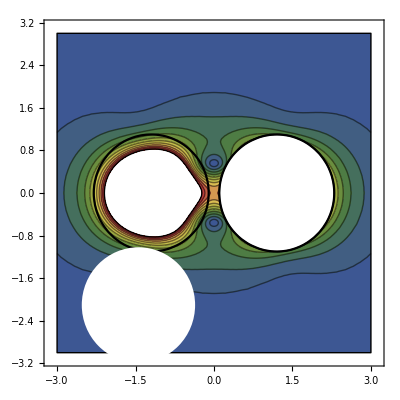

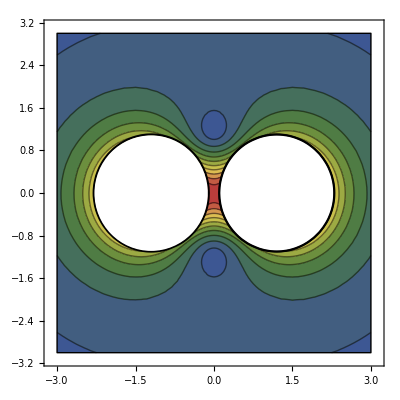

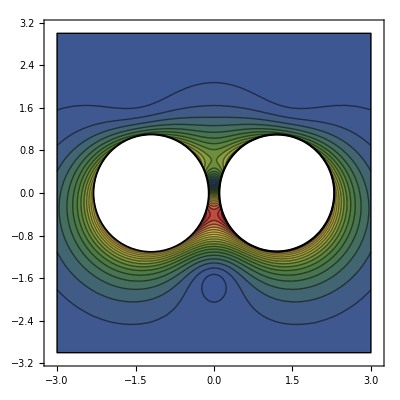

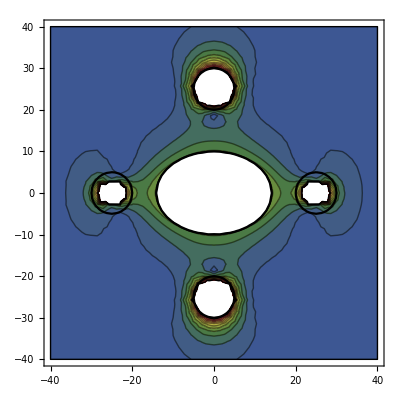

```mathematica
ContourPlot[smv,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->{0,},Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1]
```

x+ⅈ y

4

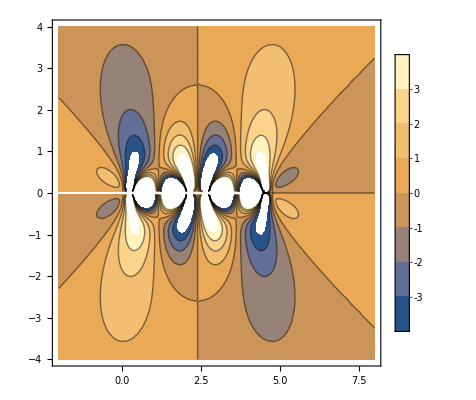

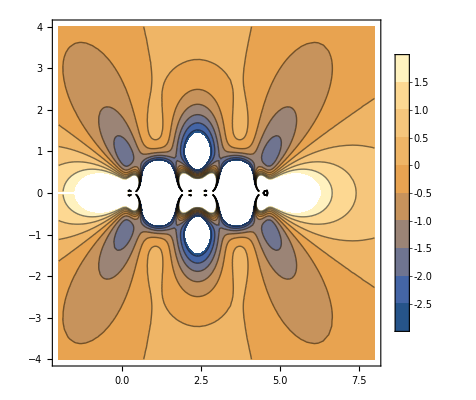

```mathematica
Clear[r,z]
r=Alpha0z;
z=x+I*y
size=4

ContourPlot[Im[r],{x,-size/2,2size},{y,-size,size},PlotLegends->Automatic]
ContourPlot[Re[r],{x,-size/2,2size},{y,-size,size},PlotLegends->Automatic]
```

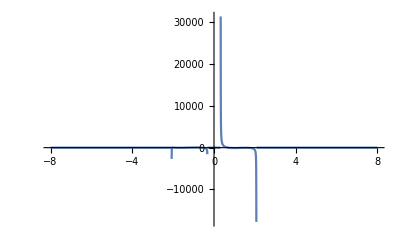

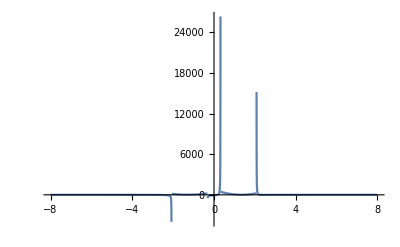

```mathematica
Plot[Re[r],{z,-8,8},PlotRange->All]
Plot[Im[r],{z,-8,8},PlotRange->All]
```

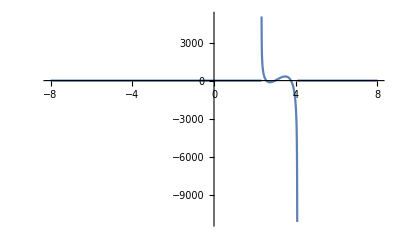

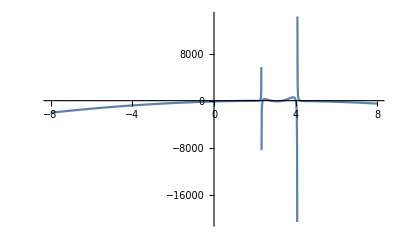

```mathematica
rq=Alpha0[1];
Xi=XiQ[1];
z=x+I*y;
rq
Plot[Re[rq],{z,-8,8},PlotRange->All]
Plot[Im[rq],{z,-8,8},PlotRange->All]
```

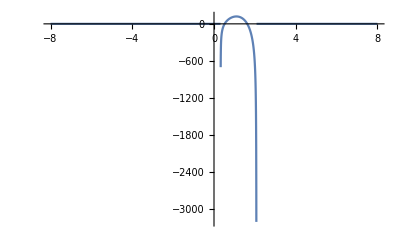

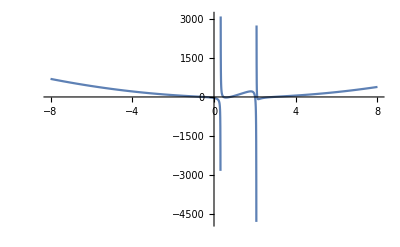

```mathematica
rq2=Alpha0[2];
Xi=XiQ[2];

Plot[Re[rq2],{z,-8,8},PlotRange->All]
Plot[Im[rq2],{z,-8,8},PlotRange->All]
```

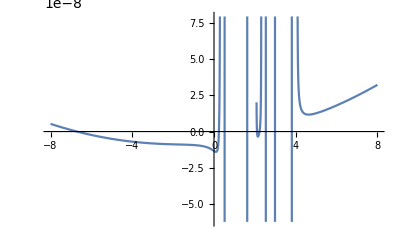

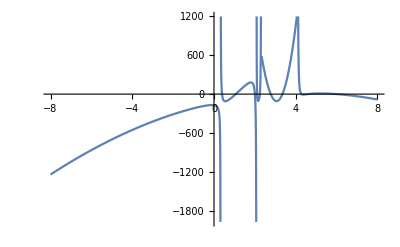

```mathematica
Plot[Re[rq2]+Re[rq],{z,-8,8}]
Plot[Im[rq2]+Im[rq],{z,-8,8}]
```

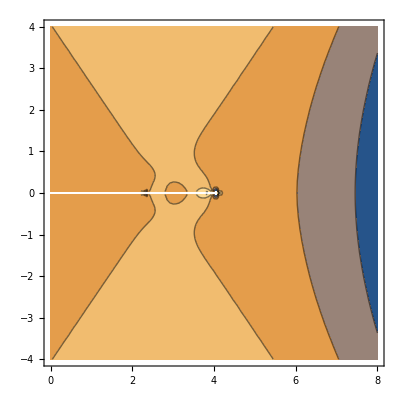

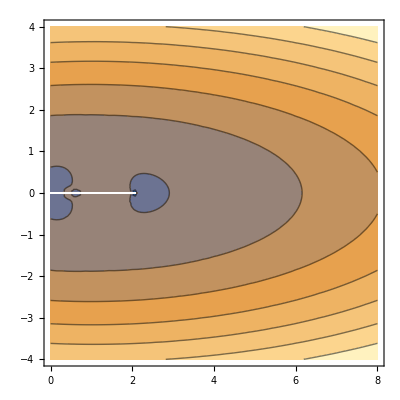

```mathematica
size=4;
ContourPlot[Im[rq],{x,-0size,2size},{y,-size,size}]
ContourPlot[Im[rq2],{x,-0size,2size},{y,-size,size}]
```

```mathematica
Snq[2,1]
Snq[2,2]
```

-3.38126×10^-16-2.08024 ⅈ

1.11562×10^-16+2.08024 ⅈ

```mathematica
p=2;q=1;
Sum[Snq[m,p]smnpq[m,2,p,q],{m,n}]
```

-2.27753×10^-17+0.213003 ⅈ

```mathematica
Clear[p,q,i,f12,f22]
p=1;
q=2;
i=1;
f12=Fn[i,q]+Sum[Snq[m,p]smnpq[m,i,p,q],{m,n}]
i=2;
f22=Fn[i,q]+Sum[Snq[m,p]smnpq[m,i,p,q],{m,n}]
```

4.87183×10^-17+5.34465 ⅈ

-1.14232×10^-17-0.213003 ⅈ

```mathematica
fnq[1,q]
fnq[2,q]
```

4.87183×10^-17+5.34465 ⅈ

-1.14232×10^-17-0.213003 ⅈ

```mathematica
fnq[1,p]
fnq[2,p]
```

-1.03655×10^-16+5.34465 ⅈ

-2.27753×10^-17+0.213003 ⅈ

```mathematica
Clear[p,q,i,f11,f21]
p=2;
q=1;
i=1;
f11=Fn[i,q]+Sum[Snq[m,p]smnpq[m,i,p,q],{m,n}]
i=2;
f21=Fn[i,q]+Sum[Snq[m,p]smnpq[m,i,p,q],{m,n}]
i=3;
f31=Fn[i,q]+Sum[Snq[m,p]smnpq[m,i,p,q],{m,n}]
```

-1.03655×10^-16+5.34465 ⅈ

-2.27753×10^-17+0.213003 ⅈ

-5.2479×10^-18+0.0494416 ⅈ

```mathematica
Clear[Rmnpq,f1]
MatrixCreate[Rmnpq,smnpq,n,ntot];
f1= Rmnpq.STem 
VecRev[f1,fnq1,n,ntot];
```

{-1.03655×10^-16+0.956879 ⅈ,-2.27753×10^-17+0.213003 ⅈ,-5.2479×10^-18+0.0494416 ⅈ,4.87183×10^-17+0.956879 ⅈ,-1.14232×10^-17-0.213003 ⅈ,2.77797×10^-18+0.0494416 ⅈ}

```mathematica
f1
```

{9.48966×10^-18+0.93187 ⅈ,4.38359×10^-18+0.409155 ⅈ,1.5771×10^-18+0.140523 ⅈ,-6.93565×10^-17+0.93187 ⅈ,-2.01981×10^-17-0.409155 ⅈ,-4.45132×10^-17+0.140523 ⅈ}

```mathematica
i=1;
q=1;
Fn[i,q]+fnq1[i,q]
i=2;
Fn[i,q]+fnq1[i,q]
```

9.48966×10^-18+5.31964 ⅈ

4.38359×10^-18+0.409155 ⅈ

```mathematica
i=1;
q=2;
Fn[i,q]+fnq1[i,q]
i=2;
Fn[i,q]+fnq1[i,q]
```

-6.93565×10^-17+5.31964 ⅈ

-2.01981×10^-17-0.409155 ⅈ

```mathematica
MatrixCreate[matname,Amnpq,n,ntot]
```

```mathematica
MatrixForm[matname]
```

(Amnpq[1,1,1,1] | Amnpq[2,1,1,1] | Amnpq[3,1,1,1] | Amnpq[1,1,2,1] | Amnpq[2,1,2,1] | Amnpq[3,1,2,1]
Amnpq[1,2,1,1] | Amnpq[2,2,1,1] | Amnpq[3,2,1,1] | Amnpq[1,2,2,1] | Amnpq[2,2,2,1] | Amnpq[3,2,2,1]
Amnpq[1,3,1,1] | Amnpq[2,3,1,1] | Amnpq[3,3,1,1] | Amnpq[1,3,2,1] | Amnpq[2,3,2,1] | Amnpq[3,3,2,1]
Amnpq[1,1,1,2] | Amnpq[2,1,1,2] | Amnpq[3,1,1,2] | Amnpq[1,1,2,2] | Amnpq[2,1,2,2] | Amnpq[3,1,2,2]
Amnpq[1,2,1,2] | Amnpq[2,2,1,2] | Amnpq[3,2,1,2] | Amnpq[1,2,2,2] | Amnpq[2,2,2,2] | Amnpq[3,2,2,2]
Amnpq[1,3,1,2] | Amnpq[2,3,1,2] | Amnpq[3,3,1,2] | Amnpq[1,3,2,2] | Amnpq[2,3,2,2] | Amnpq[3,3,2,2])

```mathematica
Dimensions[matname]
```

{6,6}

```mathematica
VecCreate[funcname,func,n,ntot]
```

```mathematica
funcname
```

{func[1,1],func[2,1],func[3,1],func[1,2],func[2,2],func[3,2]}

```mathematica
matname.funcname
```

{Amnpq[1,1,1,1] func[1,1]+Amnpq[1,1,2,1] func[1,2]+Amnpq[2,1,1,1] func[2,1]+Amnpq[2,1,2,1] func[2,2]+Amnpq[3,1,1,1] func[3,1]+Amnpq[3,1,2,1] func[3,2],Amnpq[1,2,1,1] func[1,1]+Amnpq[1,2,2,1] func[1,2]+Amnpq[2,2,1,1] func[2,1]+Amnpq[2,2,2,1] func[2,2]+Amnpq[3,2,1,1] func[3,1]+Amnpq[3,2,2,1] func[3,2],Amnpq[1,3,1,1] func[1,1]+Amnpq[1,3,2,1] func[1,2]+Amnpq[2,3,1,1] func[2,1]+Amnpq[2,3,2,1] func[2,2]+Amnpq[3,3,1,1] func[3,1]+Amnpq[3,3,2,1] func[3,2],Amnpq[1,1,1,2] func[1,1]+Amnpq[1,1,2,2] func[1,2]+Amnpq[2,1,1,2] func[2,1]+Amnpq[2,1,2,2] func[2,2]+Amnpq[3,1,1,2] func[3,1]+Amnpq[3,1,2,2] func[3,2],Amnpq[1,2,1,2] func[1,1]+Amnpq[1,2,2,2] func[1,2]+Amnpq[2,2,1,2] func[2,1]+Amnpq[2,2,2,2] func[2,2]+Amnpq[3,2,1,2] func[3,1]+Amnpq[3,2,2,2] func[3,2],Amnpq[1,3,1,2] func[1,1]+Amnpq[1,3,2,2] func[1,2]+Amnpq[2,3,1,2] func[2,1]+Amnpq[2,3,2,2] func[2,2]+Amnpq[3,3,1,2] func[3,1]+Amnpq[3,3,2,2] func[3,2]}

```mathematica
Clear[p,q,i,f11,f21]

q=1;
i=2;
f11=Sum[Sum[func[m,p]Amnpq[m,i,p,q],{m,n}],{p,ntot}]
```

Amnpq[1,2,1,1] func[1,1]+Amnpq[1,2,2,1] func[1,2]+Amnpq[2,2,1,1] func[2,1]+Amnpq[2,2,2,1] func[2,2]+Amnpq[3,2,1,1] func[3,1]+Amnpq[3,2,2,1] func[3,2]

```mathematica
Clear[p,q,i,f11,f21]
p=2;
q=1;
i=2;
f11=Sum[func[m,p]Amnpq[m,i,p,q],{m,n}]
```

Amnpq[1,2,2,1] func[1,2]+Amnpq[2,2,2,1] func[2,2]+Amnpq[3,2,2,1] func[3,2]

```mathematica
{{aa1,aa2},{aa3,aa4}}.{bb1,bb2}
```

{aa1 bb1+aa2 bb2,aa3 bb1+aa4 bb2}

```mathematica
Conjugate[{{aa1,aa2},{aa3,aa4}}].Conjugate[{bb1,bb2}]
```

{Conjugate[aa1] Conjugate[bb1]+Conjugate[aa2] Conjugate[bb2],Conjugate[aa3] Conjugate[bb1]+Conjugate[aa4] Conjugate[bb2]}

```mathematica
Clear[Rmnpq1,f11,fnq11,fTem];
MatrixCreate[Rmnpq1,smnpq,n,ntot];
f11=Rmnpq1 . STem;
VecRev[f11,fnq11,n,ntot];
MatrixForm[fTem=f11]
```

(3.45245×10^-18+0.152615 ⅈ
0.+0. ⅈ
0.+0. ⅈ
-1.80784×10^-17+0.152615 ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
Clear[Rmnpq1,f11,fnq11,fTem];
MatrixCreate[Rmnpq1,smnpq,n,ntot];
MatrixForm[Rmnpq1]
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.00965465+0. ⅈ | -0.00191589+0. ⅈ | -0.000287898+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.000957944+0. ⅈ | 0.000283327+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.00965465-1.18235×10^-18 ⅈ | 0.00191589+0. ⅈ | -0.000287898-1.05772×10^-19 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.000957944-1.17314×10^-19 ⅈ | 0.000283327+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

```mathematica
smnpq[2,2,2,1]
Eta[[2,2,2,1]]
```

0.000283327+0. ⅈ

0.000283327

```mathematica
STem
Conjugate[STem]
M1Tem.STem +M2Tem.Conjugate[STem]
```

{-9.59049×10^-16-21.169 ⅈ,-3.38126×10^-16-2.08024 ⅈ,-1.90207×10^-16-1.3327 ⅈ,-1.92963×10^-16-21.169 ⅈ,1.11562×10^-16+2.08024 ⅈ,-7.48799×10^-17-1.3327 ⅈ}

{-9.59049×10^-16+21.169 ⅈ,-3.38126×10^-16+2.08024 ⅈ,-1.90207×10^-16+1.3327 ⅈ,-1.92963×10^-16+21.169 ⅈ,1.11562×10^-16-2.08024 ⅈ,-7.48799×10^-17+1.3327 ⅈ}

{-1.52672×10^-15-8.60346 ⅈ,-2.02772×10^-16+0. ⅈ,-6.39938×10^-17+4.44089×10^-16 ⅈ,-5.82748×10^-16-8.60346 ⅈ,2.51854×10^-16+4.44089×10^-16 ⅈ,-1.55761×10^-16+2.22045×10^-16 ⅈ}

```mathematica
Clear[M1Tem11,M2Tem11,BC11, Mtem11,Tem11]

BCTem1[n_,q_]:=Module[{f},f=-(ThermalConductivityQBar[q]-1)(Fn[n,q]+Conjugate[Fn[n,q]]*v0[q]^(2n))];
M1Tem11[m_,n_,p_,q_]:=Module[{f,f1,f2},
f1=(ThermalConductivityQBar[q]-1)*smnpq[m,n,p,q];
f2=(ThermalConductivityQBar[q]+(v0[q]^(2n) + v0[q]^(-2n))/(v0[q]^(2n) - v0[q]^(-2n)))*KroneckerDelta[m,n]*KroneckerDelta[p,q];
f=f1+f2]

M2Tem11[m_,n_,p_,q_]:=Module[{f,f1,f2},
f1=(ThermalConductivityQBar[q]-1)*v0[q]^(2n)*Conjugate[smnpq[m,n,p,q]];
f2=(2./(v0[q]^(2n) - v0[q]^(-2n)))*KroneckerDelta[m,n]*KroneckerDelta[p,q];
f=f1+f2]
```

```mathematica
i=1;q=1;
f[i,q]
Sum[M1Tem11[m,i,p,q]*Snq[m,p]+M2Tem11[m,i,p,q]*Conjugate[Snq[m,p]],{m,n},{p,ntot}]
BCTem1[i,q]
```

f[1,1]

-1.52672×10^-15-8.60346 ⅈ

0.-8.60346 ⅈ

```mathematica
MatrixForm[Table[BCTem11[i,q],{i,n},{q,ntot}]]
```

(BCTem11[1,1] | BCTem11[1,2]
BCTem11[2,1] | BCTem11[2,2]
BCTem11[3,1] | BCTem11[3,2])

```mathematica
Clear[BCTem]
VecCreate[BCTem,BCTem1,n,ntot]
```

```mathematica
MatrixForm[BCTem]
```

(0.-8.60346 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.-8.60346 ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
M1Tem11[1,2,1,2]
```

-0.0093201+0. ⅈ

```mathematica
MatrixCreate[M1Tem,M1Tem11,n,ntot];
MatrixCreate[M2Tem,M2Tem11,n,ntot];
MatrixForm[M1Tem]
MatrixForm[M2Tem]
```

(1.25752+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.0429719+5.26253×10^-18 ⅈ | -0.0186402+0. ⅈ | 0.00632714+2.32455×10^-18 ⅈ
0.+0. ⅈ | 1.02637+0. ⅈ | 0.+0. ⅈ | 0.0093201+1.14138×10^-18 ⅈ | -0.00589774+0. ⅈ | 0.00257933+9.4763×10^-19 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.00297+0. ⅈ | 0.00210905+2.58284×10^-19 ⅈ | -0.00171955+0. ⅈ | 0.000914068+3.35823×10^-19 ⅈ
0.0429719+0. ⅈ | 0.0186402+0. ⅈ | 0.00632714+0. ⅈ | 1.25752+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.0093201+0. ⅈ | -0.00589774+0. ⅈ | -0.00257933+0. ⅈ | 0.+0. ⅈ | 1.02637+0. ⅈ | 0.+0. ⅈ
0.00210905+0. ⅈ | 0.00171955+0. ⅈ | 0.000914068+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.00297+0. ⅈ)

(0.762475+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.12723-1.55812×10^-17 ⅈ | -0.0551896+0. ⅈ | 0.0187333-6.8825×10^-18 ⅈ
0.+0. ⅈ | 0.231156+0. ⅈ | 0.+0. ⅈ | 0.0817023-1.00056×10^-17 ⅈ | -0.051701+0. ⅈ | 0.022611-8.30716×10^-18 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.0771711+0. ⅈ | 0.0547402-6.70374×10^-18 ⅈ | -0.0446309+0. ⅈ | 0.0237246-8.71628×10^-18 ⅈ
0.12723+0. ⅈ | 0.0551896+0. ⅈ | 0.0187333+0. ⅈ | 0.762475+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.0817023+0. ⅈ | -0.051701+0. ⅈ | -0.022611+0. ⅈ | 0.+0. ⅈ | 0.231156+0. ⅈ | 0.+0. ⅈ
0.0547402+0. ⅈ | 0.0446309+0. ⅈ | 0.0237246+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.0771711+0. ⅈ)

```mathematica
RealMTem = M1Tem+M2Tem;
ImMTem = M1Tem-M2Tem;
```

```mathematica
MatrixForm[RealMTem]
MatrixForm[ImMTem]
```

(2.02+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.170202-1.03187×10^-17 ⅈ | -0.0738298+0. ⅈ | 0.0250604-4.55795×10^-18 ⅈ
0.+0. ⅈ | 1.25752+0. ⅈ | 0.+0. ⅈ | 0.0910224-8.86426×10^-18 ⅈ | -0.0575988+0. ⅈ | 0.0251904-7.35953×10^-18 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.08014+0. ⅈ | 0.0568492-6.44545×10^-18 ⅈ | -0.0463505+0. ⅈ | 0.0246387-8.38045×10^-18 ⅈ
0.170202+0. ⅈ | 0.0738298+0. ⅈ | 0.0250604+0. ⅈ | 2.02+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.0910224+0. ⅈ | -0.0575988+0. ⅈ | -0.0251904+0. ⅈ | 0.+0. ⅈ | 1.25752+0. ⅈ | 0.+0. ⅈ
0.0568492+0. ⅈ | 0.0463505+0. ⅈ | 0.0246387+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.08014+0. ⅈ)

(0.49505+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0842585+2.08438×10^-17 ⅈ | 0.0365494+0. ⅈ | -0.0124061+9.20705×10^-18 ⅈ
0.+0. ⅈ | 0.795213+0. ⅈ | 0.+0. ⅈ | -0.0723822+1.1147×10^-17 ⅈ | 0.0458033+0. ⅈ | -0.0200317+9.25479×10^-18 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.925802+0. ⅈ | -0.0526311+6.96202×10^-18 ⅈ | 0.0429114+0. ⅈ | -0.0228105+9.0521×10^-18 ⅈ
-0.0842585+0. ⅈ | -0.0365494+0. ⅈ | -0.0124061+0. ⅈ | 0.49505+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0723822+0. ⅈ | 0.0458033+0. ⅈ | 0.0200317+0. ⅈ | 0.+0. ⅈ | 0.795213+0. ⅈ | 0.+0. ⅈ
-0.0526311+0. ⅈ | -0.0429114+0. ⅈ | -0.0228105+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.925802+0. ⅈ)

```mathematica
LinearSolve[RealMTem,Re[BCTem] ]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
LinearSolve[ImMTem,Im[BCTem] ]
```

{-21.169+9.59049×10^-16 ⅈ,-2.08024+3.38126×10^-16 ⅈ,-1.3327+1.90207×10^-16 ⅈ,-21.169+1.92963×10^-16 ⅈ,2.08024-1.11562×10^-16 ⅈ,-1.3327+7.48799×10^-17 ⅈ}

```mathematica
mnpq
```

0.0429719+0. ⅈ

```mathematica
m=1;i=2;
p=2;q=1;
smnpq[m,i,p,q]
f1=(ThermalConductivityQBar[q]-1)*smnpq[m,i,p,q]
f2=(ThermalConductivityQBar[q]+(v0[q]^(2i) + v0[q]^(-2i))/(v0[q]^(2i) - v0[q]^(-2i)))*KroneckerDelta[m,i]*KroneckerDelta[p,q]
```

-0.0093201-1.14138×10^-18 ⅈ

0.0093201+1.14138×10^-18 ⅈ

0.

```mathematica
m=1;i=1;
Eta[[m,Abs[i],1,2]]
Eta[[m,Abs[i],2,1]]
```

-0.0429719+0. ⅈ

-0.0429719-5.26253×10^-18 ⅈ

```mathematica
Clear[bcTem1nqt,bcTem2nqt]
bcTem1nqt[n_,q_]:=Module[{f,f1,f2,f3,f4},
f1=Bettal0*dd[q]/n/2.;
f2=-BettalQ[q]*dd[q]/n/2.;
f3=(fnq[n+1,q]-fnq[n-1,q]) - (Snq[n-1,q]-Snq[n+1,q])- Snq[1,q]((-v0[q])^(n));
f4=Gnq[n+1,q]-Gnq[n-1,q];
f=f1*f3+f2*f4]

bcTem2nqt[n_,q_]:=Module[{f,f0,f1,f2,f3,f4},
f0=v0[q]^(2n);
f1=Bettal0*dd[q]/n/2.;
f2=-BettalQ[q]*dd[q]/n/2.;
f3=(fnq[n-1,q]-fnq[n+1,q]) f0 - Snq[1,q]((-v0[q])^(n));
f4=(Gnq[n-1,q]-Gnq[n+1,q]) f0;
f=f1*f3+f2*f4]
```

```mathematica
Table[bcTem1nqt[i,1],{i,n}]
Table[bcTem1nqt[i,2],{i,n}]
```

{26.3263-0.0422427 ⅈ,-1.46305×10^-17+0.703767 ⅈ,-1.68069×10^-18+0.014026 ⅈ}

{26.3263+0.0421593 ⅈ,3.67038×10^-22+0.703771 ⅈ,-4.11915×10^-22-0.014108 ⅈ}

```mathematica
Table[bcTem1nqt[i,1],{i,n}]
Table[bcTem1nqt[i,2],{i,n}]
```

{26.3263-0.0422427 ⅈ,-1.46305×10^-17+0.703767 ⅈ,-1.68069×10^-18+0.014026 ⅈ}

{26.3263+0.0421593 ⅈ,3.67038×10^-22+0.703771 ⅈ,-4.11915×10^-22-0.014108 ⅈ}

```mathematica
Table[bcTem2nqt[i,1],{i,n}]
Table[bcTem2nqt[i,2],{i,n}]
```

{-77.9464+0.1249 ⅈ,1.28274×10^-16-6.16894 ⅈ,4.35755×10^-17-0.36513 ⅈ}

{-77.9464-0.124982 ⅈ,5.55605×10^-22-6.16898 ⅈ,-4.86581×10^-22+0.365045 ⅈ}

```mathematica
fnq[3,1]
fnq[3,2]
```

0.+0. ⅈ

0.+0. ⅈ

```mathematica
Gnq[0,1]
Gnq[0,2]
```

300.+0. ⅈ

300.+0. ⅈ

```mathematica
Clear[f,f0,f1,f2,f3,f4,i]
i=1;q=2;
f0=v0[q]^(2i);
f1=Bettal0*dd[q]/i/2.;
f2=-BettalQ[q]*dd[q]/i/2.;
f3=(fnq[i-1,q]-fnq[i+1,q]) f0 - Snq[1,q]((-v0[q])^(i));
Gnq[i-1,q]
Gnq[i+1,q]
f4=(Gnq[i-1,q]-Gnq[i+1,q]) f0;
f=f1*f3;
f2*f4;
```

300.+0. ⅈ

-1.28945×10^-28-0.480867 ⅈ

```mathematica
Snmpq[n,m,p,q]
```

Snmpq[3,m,p,2]

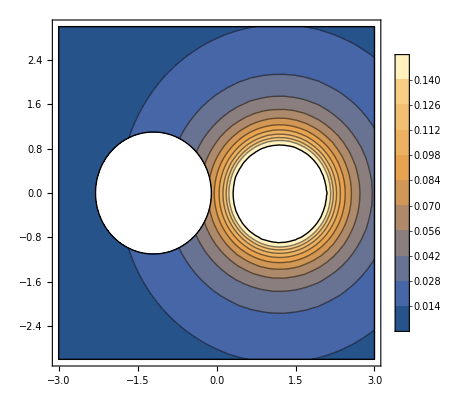

{2.24705-0.00466549 ⅈ,0.+0.346565 ⅈ,0.-34.212 ⅈ}

{-49432.9-0.00466549 ⅈ,0.-268823. ⅈ,0.-34.212 ⅈ}

```mathematica
Clear[Sigma11zt,Sigma22zt,Sigma12zt]
Clear[zp,zq,Xi,z]
Sigma11zt[i_]:=Module[{f,f1,f2,f3},f3=Sigma11mStress[i]Cos[Theta[i]]^2-2 Sigma12mStress[i] Cos[Theta[i]] Sin[Theta[i]]+Sigma22mStress[i] Sin[Theta[i]]^2;
f=f3];

Sigma12zt[i_]:=Module[{f,f1,f2,f3},f3=Sigma12mStress[i] Cos[2 Theta[i]]+(Sigma11mStress[i]-Sigma22mStress[i]) Cos[Theta[i]] Sin[Theta[i]];
f=f3];

Sigma22zt[i_]:=Module[{f,f1,f2,f3},f3=Sigma22mStress[i] Cos[Theta[i]]^2+Sigma11mStress[i] Sin[Theta[i]]^2+Sigma12mStress[i] Sin[2 Theta[i]];
f=f3];

Sigma11Ztot[i_]:=Module[{f,f1,f2,f3,f4},Clear[z,zp,zq,Xi];
f1=Sigma11zt[i];
f2=f1;
Xi=XiQ[i];
z=x+I y;
f3=f2]
Sigma12Ztot[i_]:=Module[{f,f1,f2,f3,f4},Clear[z,zp,zq,Xi];
f1=Sigma12zt[i];
f2=f1;
Xi=XiQ[i];
z=x+I y;
f3=f2]
Sigma22Ztot[i_]:=Module[{f,f1,f2,f3,f4},Clear[z,zp,zq,Xi];
f1=Sigma22zt[i];
f2=f1;
Xi=XiQ[i];
z=x+I y;
f3=f2]


Clear[size, size2,size2p,size3,q]
Clear[r11,r12,r22,rt,Xi,z,q]
c1=10;
c2=4;
q=1;
size=3;
size2=0Re[zcenter[q]]-1.5* l1[q];
size2p=0Re[zcenter[q]]+1.5* l1[q];
size3=1.5 l2[q];



(*r11=Sigma11Ztot[q]+Sigma11Ztot[q+1];
r12=Sigma12Ztot[q]+Sigma12Ztot[q+1];
r22=Sigma22Ztot[q]+Sigma22Ztot[q+1];*)
r11=Sigma11zt[q];
r12=Sigma12zt[q];
r22=Sigma22zt[q];
(*r11=Sigma11mStress[q];
r12=Sigma12mStress[q];
r22=Sigma22mStress[q];*)
rmv = Sqrt[r11*r11+r22*r22-r11*r22+3r12*r12];


Xi=XiQ[q];ArcCosh[z/Dq[q]];
z=x+I y;
Clear[rmv1]
rmv1=rmv;

Clear[q,z,Xi,rmvtrmv2]
q=2;
Xi=XiQ[q];ArcCosh[z/Dq[q]];
z=x+I y;
rmv2=rmv;

rmvt=rmv1+rmv2;
ContourPlot[rmv1,{x,-size,size},{y,-size,size},BoundaryStyle->Black,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1],ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic]



Table[bcTem1nq[i,1],{i,n}]
Table[bcTem2nq[i,1],{i,n}]
```

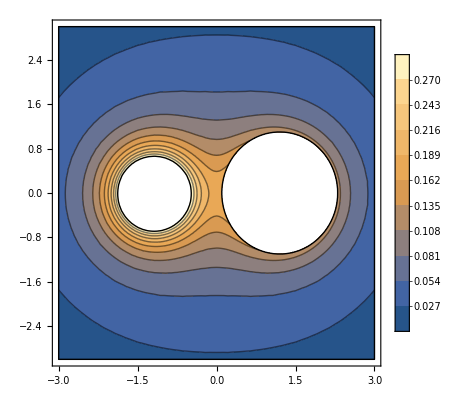

```mathematica
ContourPlot[rmvt,{x,-size,size},{y,-size,size},BoundaryStyle->Black,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1],ContourLabels->False, Exclusions->None,Contours->c1,PlotLegends->Automatic, PlotRange->{0,0.30}]
```

```mathematica
Print["a"]
Table[a[i,1],{i,n}]
Table[a[i,2],{i,n}]
Print["b"]
Table[b[i,1],{i,n}]
Table[b[i,2],{i,n}]
Print["c"]
Table[c[i,1],{i,n}]
Table[c[i,2],{i,n}]
Print["d"]
Table[d[i,1],{i,n}]
Table[d[i,2],{i,n}]
```

a

{-6.44786×10^-6+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{a[1,2],a[2,2],a[3,2]}

b

{-6.44786×10^-6+2.22045×10^-16 ⅈ,0.-9.31323×10^-10 ⅈ,0.+0. ⅈ}

{b[1,2],b[2,2],b[3,2]}

c

{-0.703393+0.000167704 ⅈ,0.-0.366537 ⅈ,0.+3.38795×10^-8 ⅈ}

{c[1,2],c[2,2],c[3,2]}

d

{-1546.76+0.36811 ⅈ,0.-1612.03 ⅈ,0.+0.000223402 ⅈ}

{d[1,2],d[2,2],d[3,2]}

```mathematica
LinearSolve[abar,bcbar]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.8,0.,-4.8356×10^6,2199.,0.,0.,0.,0.,0.,0.,«14»},{0.,1.,6597.,-1.,0.,0.,0.,0.,0.,0.,«14»},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«14»},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,«14»},{0.,0.,0.,0.,1.8,0.,-2.1267×10^10,4.8356×10^6,0.,0.,«14»},{«1»},{0.,0.,«7»,0.,«14»},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,«14»},{0.,0.,0.,0.,0.,0.,0.,0.,1.8,0.,«14»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,«14»},«14»} may contain significant numerical errors.

{-6.44786×10^-6,-6.44786×10^-6,-0.703393,-1546.76,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.22045×10^-16,0.000167704,0.36811,0.,-9.31323×10^-10,-0.366537,-1612.03,0.,0.,3.38795×10^-8,0.000223402}

```mathematica
c[1,1]
```

-0.703393+0.000167704 ⅈ

```mathematica
Alpha0[1]
```

55. ⅇ^(-Conjugate[Xi]) Conjugate[Csch[Xi]]+ⅇ^(-2 Xi) Csch[Xi] ((0.-0.0158883 ⅈ)+(55.+1.89403×10^-9 ⅈ) ⅇ^Xi+(0.0468935+0. ⅈ) ⅇ^Xi Conjugate[Cosh[Xi]] (1172.87+1172.87 Coth[Xi]) Csch[Xi]+((-120890.-8.61307×10^-22 ⅈ)-(55.+0. ⅈ) ⅇ^Xi Cosh[Xi]+(-60445.+27.4875 ⅇ^(2 Xi)-(55.+0. ⅈ) ⅇ^Xi Cosh[Xi]) Coth[Xi]) Csch[Xi])

```mathematica
Alpha0[1]
```

((440.+0. ⅈ) ⅇ^(3 Xi) Conjugate[Cosh[Xi]])/((-1.+1. ⅇ^(2 Xi))^3)+55. ⅇ^(-Conjugate[Xi]) Conjugate[Csch[Xi]]+(241890.-725450. ⅇ^(2 Xi)+219.95 ⅇ^(4 Xi)-(440.+0. ⅈ) ⅇ^(3 Xi) Cosh[Xi])/((-1.+1. ⅇ^(2 Xi))^3)

```mathematica
r=Beta0[1]+Alpha0[1];
rr=BetaFar[1]+AlphaFar[1]
Xi=XiQ[1];
z=x+I*y;
```

0.

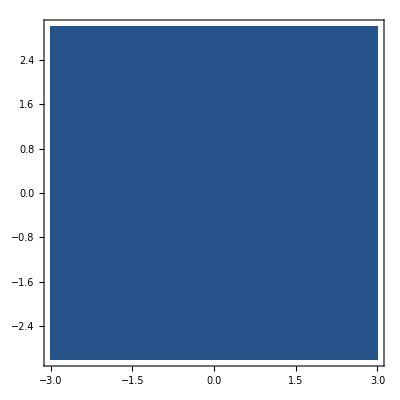

-Graphics-

```mathematica
ContourPlot[Re[rr],{x,-3,3},{y,-3,3}]
ContourPlot[Im[rr],{x,-3,3},{y,-3,3}]
```

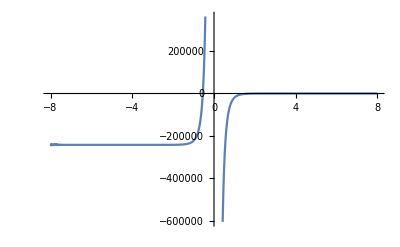

```mathematica
Plot[%27,{Xi,-8,8}]
```

```mathematica
Phi0::usage=" Phi is a scalar Muskhelishvili potential of complex variable method in plane Elasticity. zero suffix functions denote potentials in the matrix host."; 
Psi0::usage=" Phi and Psi are scalar Muskhelishvili potentials of complex variable method in plane Elasticity. zero suffix functions denote potentials in the matrix host."; 
Tau0::usage=" Traction field. zero suffix functions denote potentials in the matrix host."; 
TauFar::usage=" Traction field with far field source"; 
Alpha0::usage=" α = σ11 - I σ12, zero suffix functions denote potentials in the matrix host."; 
AlphaFar::usage=" α = σ11 - I σ12, Far suffix denote fields in the matrix host.";
PhiFarQ::usage=" Phi scalar potential associated with the far-field load at qth coordinate system."; 
PsiFarQ::usage=" Psi scalar potential associated with the far-field load at qth coordinate system.";
Beta0::usage=" β = σ11 + σ22, zero suffix functions denote field with far field source"; 
BetaFar::usage=" β = σ11 + σ22, zero suffix functions denote field with far field source";
```

```mathematica
PhiQs[q_]: " Phi and Psi are scalar Muskhelishvili potentials of complex variable method in plane Elasticity. Q suffix functions denote potentials calculated in qth coordinate system. s and r suffix denote the singular and regular field calculateions. PQr means calculating regular fields at qth coordinate system due to the presence of pth inclusion. FarQ suffix indicates that potentials are associated with the far-field load at qth coordinate system."; 
PsiQs[q_]
PhiPQr[p_, q_]
PsiPQr[p_, q_]
PhiFarQ[q_]
PsiFarQ[q_]
Omegaprim[q_]: "It is derivitive of Omega with respect to z."
```

```mathematica
Phi0z::usage=" Phi is a scalar Muskhelishvili potential of complex variable method in plane elasticity. zero suffix functions denote potentials in the matrix host. z suffix indicates that fields are calculated in z coordinate system."; 
Psi0z::usage=" Phi and Psi are scalar Muskhelishvili potentials of complex variable method in plane Elasticity. zero suffix functions denote potentials in the matrix host.z suffix indicates that fields are calculated in z coordinate system."; 

Alpha0z::usage=" α = σ11 - I σ12, zero suffix functions denote potentials in the matrix host. z suffix indicates that fields are calculated in z coordinate system."; 
AlphaFarz::usage=" α = σ11 - I σ12, Far suffix denote fields in the matrix host. z suffix indicates that fields are calculated in z coordinate system.";
PhiFarQz::usage=" Phi scalar potential associated with the far-field load at z coordinate system."; 
PsiFarQz::usage=" Psi scalar potential associated with the far-field load at z coordinate system.";
Beta0z::usage=" β = σ11 + σ22, zero suffix functions denote field with far field source. z suffix indicates that fields are calculated in z coordinate system."; 
BetaFarz::usage=" β = σ11 + σ22, zero suffix functions denote field with far field source. z suffix indicates that fields are calculated in z coordinate system.";
```

```mathematica
Sigma11ztot::usage=" Sigma11ztot is the total Sigma11 stresses in the matrix material at z coordinate system. "
Sigma12ztot::usage=" Sigma12ztot is the total Sigma11 stresses in the matrix material at z coordinate system. "
Sigma2ztot::usage=" Sigma22ztot is the total Sigma11 stresses in the matrix material at z coordinate system. "
```

```mathematica
PhiQInside::usage=" Phi is a scalar Muskhelishvili potential of complex variable method in plane elasticity. QInside suffix functions denote potentials in the inclusion. z suffix indicates that fields are calculated in z coordinate system."; 
PsiQInside::usage=" Phi and Psi are scalar Muskhelishvili potentials of complex variable method in plane Elasticity. QInside suffix functions denote potentials in the inclusion. z suffix indicates that fields are calculated in z coordinate system."; 

AlphaQ::usage=" α = σ11 - I σ12, zero suffix functions denote potentials in the matrix host. Q suffix indicates that fields are calculated in z coordinate system inside inclusion Q."; 

BetaQ::usage=" β = σ11 + σ22, zero suffix functions denote field with far field source. Q suffix indicates that fields are calculated in z coordinate system inside inclusion Q.";
```